```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
tMin=-1;
```

```mathematica
(* n = -1 luego 
(Y[t])^((n-1)/2) ----> Y^-1
*)
```

```mathematica
sol=NDSolve[{Y'[t]==v[t],v'[t]==2*Cxi[1/10]*(Y[t])^(-1),Y[ti]==1,v[ti]==2*Hti,WhenEvent[Y[t]==0,"StopIntegration","LocationMethod"->"Brent"]},{Y,v},{t,tMin,ti},WorkingPrecision->40,AccuracyGoal->25,PrecisionGoal->25,MaxStepSize->1/1000,MaxSteps->Infinity];
```

```mathematica
apos1[t_]:=ai*Sqrt[Y[t]/. sol[[1]]];
aneg1[t_]:=-ai*Sqrt[Y[t]/. sol[[1]]];
```

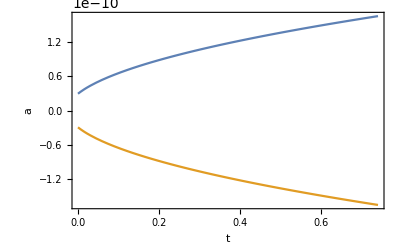

```mathematica
Plot[{apos1[t],aneg1[t]}, {t, 0, ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
```

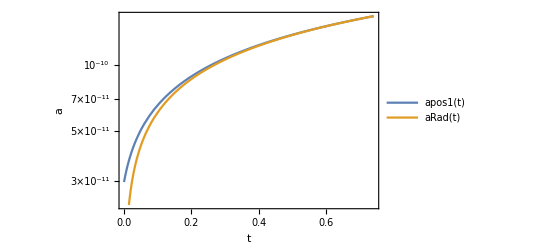

```mathematica
LogPlot[{apos1[t], aRad[t]}, {t, 0, ti}, PlotLegends->"Expressions", AxesLabel->{t,a},Frame->True, PlotRangePadding->0]
```

```mathematica
tBB:= (Y/. sol[[1]])["Domain"][[1,1]]
```

```mathematica
tBB
```

-1.

```mathematica
aposf[t_]:=ai*Sqrt[Y[t+tBB]/. sol[[1]]];anegf[t_]:=-ai*Sqrt[Y[t+tBB]/. sol[[1]]];
```

InterpolatingFunction::dmval: Input value {-1.73997} lies outside the range of data in the interpolating function. Extrapolation will be used.

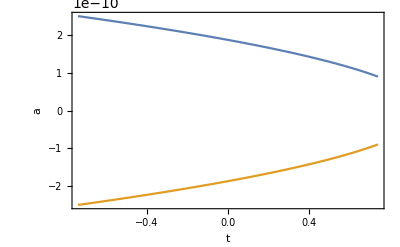

```mathematica
Plot[{aposf[t],anegf[t]}, {t, -ti, ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0]
```

InterpolatingFunction::dmval: Input value {-0.83997} lies outside the range of data in the interpolating function. Extrapolation will be used.

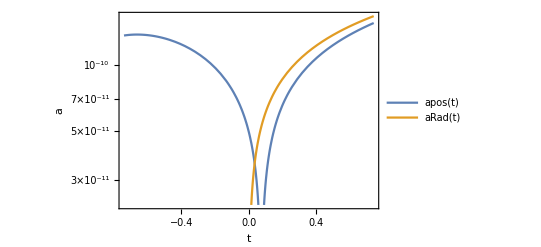

```mathematica
LogPlot[{apos[t], aRad[t]}, {t, -ti, ti}, PlotLegends->"Expressions", AxesLabel->{t,a}, Frame->True, PlotRangePadding->0]
```

```mathematica
vFunc=v/. sol[[1]];
```

```mathematica
tBounce=t/. FindRoot[vFunc[t]==0,{t,0}];
tBounce
```

-0.0268961

```mathematica
apos[t_]:=ai*Sqrt[Y[t+tBounce]/. sol[[1]]];
aneg[t_]:=-ai*Sqrt[Y[t+tBounce]/. sol[[1]]]
```

```mathematica
apos[0]
```

8.82596×10^-15

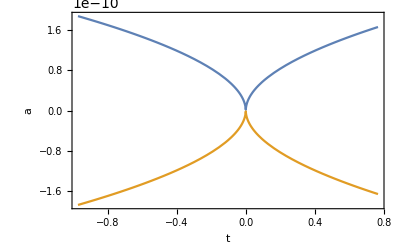

```mathematica
Plot[{apos[t],aneg[t]},{t,tMin-tBounce,ti-tBounce},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

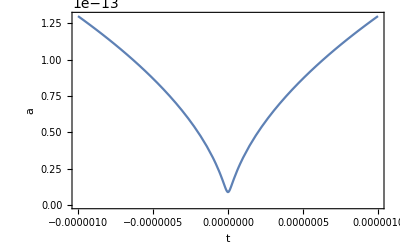

```mathematica
Plot[{apos[t]},{t,-0.000001,0.000001},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

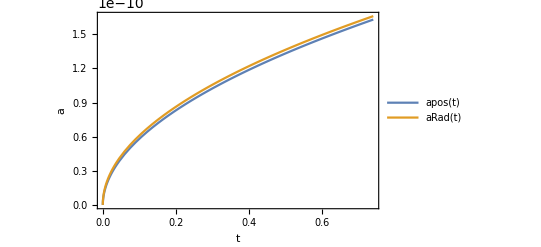

```mathematica
Plot[{apos[t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```

```mathematica
ρbh[t_]:= ρ0[1/10]*(ai/apos[t])^4
```

```mathematica
Plot[ρbh[t],{t,tMin-tBounce,ti-tBounce},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
ρbh[0]
```

9.17416×10^42

```mathematica
ρbh[10^(-4)]
```

8.65604×10^33

```mathematica
DotA[t_] := (ai^2*vFunc[t+tBounce])/(2*apos[t])
```

```mathematica
DotA[0]
```

-4.0882×10^-18

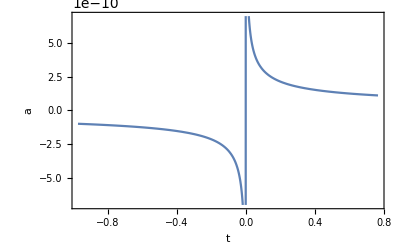

```mathematica
Plot[DotA[t],{t,tMin-tBounce,ti-tBounce},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

```mathematica
ρrad[t_]:= (3c^2)/(8π G)(DotA[t]/apos[t])^2 -ρbh[t]
```

```mathematica
Plot[ρrad[t],{t,tMin-tBounce,ti-tBounce},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
ρrad[10^(-4)]
```

3.63151×10^34

```mathematica
ρrad[0]
```

-9.17416×10^42

```mathematica
ρrad[1/100000000]
```

-4.9746×10^42

```mathematica
Plot[ρrad[t],{t,-10^(-6),10^(-6)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
FindRoot[ρrad[t]==0,{t,1/100000000}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{t→6.25945×10^-8}

```mathematica
HubbleParameter[t_]:= √((8π G)/(3c^2)(ρrad[t]+ρbh[t]))
```

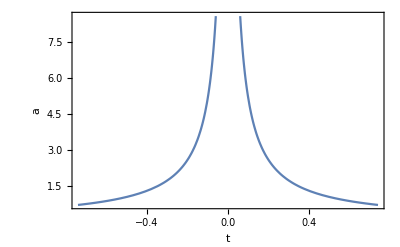

```mathematica
Plot[HubbleParameter[t],{t,-ti,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

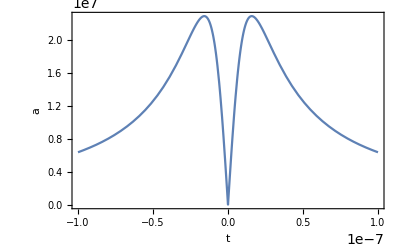

```mathematica
Plot[HubbleParameter[t],{t,-10^(-7),10^(-7)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

```mathematica
HubbleParameter[0]
```

0.

```mathematica
Plot[ρrad[t]+ρbh[t],{t,-10^(-7),10^(-7)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

```mathematica
10^(-4)
```

```mathematica
HubbleParameter[10^(-4)]
```

5289.42

```mathematica
5289.42/5000
```

1.05788

```mathematica
MHubble[t_]:= (4π c)/3*(ρrad[t]+ρbh[t])/(HubbleParameter[t])^3
```

```mathematica
Plot[MHubble[t],{t,-10^(-7),10^(-7)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
MHubble[0]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
Plot[MHubble[t],{t,-ti,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

```mathematica
N[Table[{xi,Hnum[tauForm,xi,n],rHubbleNum[tauForm,xi,n]/10^5,massHubbleNum[tauForm,xi,n]/MSun,massFormNum[tauForm,xi,n]/MSun,(massHubbleDensityNum[tauForm,xi,n]-massHubbleNum[tauForm,xi,n])/massHubbleNum[tauForm,xi,n]},{xi,xiCompareValues}],18]
```

```mathematica
γ := 0.2
Minic[t_] := γ*MHubble[t]
```

```mathematica
Minic[10^(-4)]
```

7.63217×10^33

```mathematica
Minic[10^(-4)]/MSun
```

3.83821

```mathematica
β = ρbh[10^(-4)]/(ρrad[10^(-4)]+ρbh[10^(-4)])
```

0.19248